# SetOptions

## Set option for a function

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

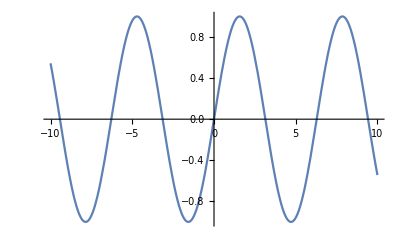

```mathematica
Plot[Sin[x],{x,-10,10}]
```

```mathematica
SetOptions[Plot,ImageSize-> 550,Frame-> All]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→All,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→550,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

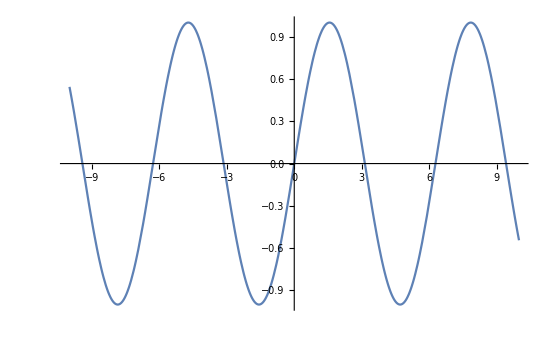

```mathematica
Plot[Sin[x],{x,-10,10}]
```

## Set option for notebooks

### Set background for current notebook

```mathematica
Options[EvaluationNotebook[]]
```

{FrontEndVersion→10.0 for Mac OS X x86 (32-bit, 64-bit Kernel) (December 4, 2014),StyleDefinitions→Default.nb,WindowMargins→{{0,Automatic},{Automatic,0}},WindowSize→{1440,851}}

```mathematica
SetOptions[
EvaluationNotebook[],
Background-> Opacity[0.98,LightYellow]
]
```

## Set option for front-end or current front-end session

### $FrontEnd

```mathematica
$FrontEnd
```

⁃ FrontEndObject ⁃

```mathematica
Options[$FrontEnd]
```

{DisplayImagePixels→Automatic,AutoOpenPalettes→{},CodeAssistOptions→{AutoPopupDelay→0.1},Current2DTool→Select,Current3DTool→RotateView,DebuggerSettings→{BreakOnAllMessages→True,ShowBreakpoints→False,ShowStack→True},Default2DTool→Select,Default3DTool→RotateView,FindSettings→{FindBoxes:>implicit,FindHistory:>{"pods","Pods",ImportConfigurationTemplateFile,TomCat,Kernel,"Short",Tagged,Florid,City,QNumberTerm,Quantity,cx,writableDirQ,$fullyResolvedPath,"Permission",$tmpDir,$TemporaryDirectory,Configuration,2008,2010,RowBox[{Sree, }],Samayamantri,KilogramsOfWaterPerKilogramsOfMoistAir,localizations,Localize,"CN",2014,RowBox[{bond, ,length}],11511,hourly},FindString→implicit,IgnoreCase→False,ReplaceBoxes→$myPath,ReplaceHistory:>{AtomicMass,$projectRootDir,$propertiesFile,ImportConfigurationPropertiesFile,myMicrosoftTranslator,MicrosoftTranslator,$fullyResolvedPath,$fullyResolvedPathToDir,"PermissionSetByStartProtectedMode",$myTemporaryDirectory,None,$myPath},SearchType→LiteralSearch,WindowMargins→{{918,-6},{345,345}},Wraparound→True},HelpViewerSettings→{WindowMargins→{{0,Automatic},{Automatic,0}},WindowSize→{1440,851}},IsPersistent2DTool→False,MessageOptions→{AllowDisablingWarnings→True,CompatibilityToolWarning→True,ConsoleMessageAction→PrintToConsole,ErrorAction→{Beep,DialogBox},ExplainBeepHelp→False,IgnoreTagBoxDeletionWarning→True,InsufficientVersionWarning→True,KernelMessageAction→PrintToNotebook,MathMLPasteWarning→True,MaxMessageCount→3,MessageCountResetTime→2.,TeXPasteWarning→True,TraditionalFormEvaluationWarning→True,UseVersionedStylesheetWarning→True,WarningAction→Beep},Parallel`Palette`Private`NotebookBrowseDirectory→/Users/meng/Dropbox/WorkSpace-Dropbox/Computing/repo-meng-lib/Mathematica/MathematicaFunction,NotebooksMenu→{InterpreterDateTest.nb→{FrontEnd`CloudObject[https://www.wolframcloud.com/objects/user-f49dcdf8-2714-42cd-b128-42ef5efd10ea/InterpreterDateTest.nb,{Name→InterpreterDateTest.nb,OwnerWolframUUID→Null,UserWolframUUID→f49dcdf8-2714-42cd-b128-42ef5efd10ea}],True,False,True},CloudDeploy.nb→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,WorkSpace-Dropbox,Computing,repo-meng-lib,Mathematica,MathematicaFunction},CloudDeploy.nb,CharacterEncoding→UTF-8],True,False,True},CloudDeploy.nb→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,WorkSpace-Dropbox,repositories,wolfram-pages,workingcopy,note,mathematica},CloudDeploy.nb,CharacterEncoding→UTF-8],True,False,True},toodledo.datatable.201503241509.m→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,WorkSpace-Dropbox,Journal,ToodledoTaskList,backup},toodledo.datatable.201503241509.m,CharacterEncoding→UTF-8],True,False,True},WeeklyReport.datatable.201503241520.m→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,repositories,wolfram-pages,workingcopy,report,progress_report,data,WolframProgressReport,WeeklyReport},WeeklyReport.datatable.201503241520.m,CharacterEncoding→UTF-8],True,False,True},WeeklyReport.datatable.201503241521.m→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,repositories,workingcopy,workingcopy,report,progress_report,data,WolframProgressReport,WeeklyReport},WeeklyReport.datatable.201503241521.m,CharacterEncoding→UTF-8],True,False,True},WeeklyReport.datatable.201503241521.m→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,repositories,wolfram-pages,workingcopy,report,progress_report,data,WolframProgressReport,WeeklyReport},WeeklyReport.datatable.201503241521.m,CharacterEncoding→UTF-8],True,False,True},WeeklyReport.datatable.201503241522.m→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,WorkSpace-Dropbox,repositories,wolfram-pages,workingcopy,report,progress_report,data,WolframProgressReport,WeeklyReport},WeeklyReport.datatable.201503241522.m,CharacterEncoding→UTF-8],True,False,True},WeeklyReport.datatable.201503241523.m→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,WorkSpace-Dropbox,repositories,wolfram-pages,workingcopy,report,progress_report,data,WeeklyReport},WeeklyReport.datatable.201503241523.m,CharacterEncoding→UTF-8],True,False,True},ToodledoTaskList.nb→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,WorkSpace-Dropbox,Journal,ToodledoTaskList},ToodledoTaskList.nb,CharacterEncoding→UTF-8],True,False,True},toodledo.datatable.m→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,WorkSpace-Dropbox,Journal,ToodledoTaskList,data},toodledo.datatable.m,CharacterEncoding→UTF-8],True,False,True},FrequentlyRunCommand-meng2maclap.nb→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,WorkSpace-Dropbox,Computing,repo-mengapps-private,Mathematica,Notebook},FrequentlyRunCommand-meng2maclap.nb,CharacterEncoding→UTF-8],True,False,True},datevalidator_outliers.nb→{FrontEnd`FileName[{$RootDirectory,Users,meng,WorkSpace-Meng2Maclap-Alpha,stash,users,meng,CloudDevelopment,optimization},datevalidator_outliers.nb,CharacterEncoding→UTF-8],True,False,True},InterpreterDateTest.nb→{FrontEnd`FileName[{$RootDirectory,Users,meng,WorkSpace-Meng2Maclap-Alpha,stash,users,meng,CloudDevelopment,optimization},InterpreterDateTest.nb,CharacterEncoding→UTF-8],True,False,True},SetOption.nb→{FrontEnd`FileName[{$RootDirectory,Users,meng,Dropbox,WorkSpace-Dropbox,Computing,repo-meng-lib,Mathematica,MathematicaFunction},SetOption.nb,CharacterEncoding→UTF-8],True,False,True}},OptionInspectorSettings→{ViewAs→Alphabetical,WindowMargins→{{0,Automatic},{Automatic,0}},WindowSize→{1440,796}},PalettesMenuSettings→{WritingAssistant.nb→{TaggingRules→{ShowWritingTools→True,ShowBasicTypesetting→False,ShowHelpLinks→False,PaletteMode→1}},ClassroomAssistant.nb→{TaggingRules→{ShowCalculator→True,ShowNavigation→False,ShowBasicCommands→False,ShowWritingTools→False,ShowBasicTypesetting→False,ShowAbcKeyboard→False,ShowHelpLinks→False,PaletteMode→1,OptionsInsertionMode→1,ShowNavigationTools→False}},BasicMathAssistant.nb→{TaggingRules→{ShowCalculator→True,ShowBasicCommands→False,ShowBasicTypesetting→True,ShowHelpLinks→False,PaletteMode→1,OptionsInsertionMode→1}},ColorSchemes.nb→{TaggingRules→{DocuToolsSettingsInternal→{$ApplicationName→Mathematica,$LinkBase→Mathematica,$ApplicationDirectory→/Users/brettc/Source/Head/Mathematica/,$DocumentationDirectory→/Users/brettc/Source/Head/Mathematica/Documentation/English/,$UseNewPageDialog→False},GradientsOpener→True,GradientsScroll→1,GradientsSelection→1,PhysicalOpener→False,PhysicalScroll→1,PhysicalSelection→1,NamedOpener→False,NamedMenu→1,IndexedOpener→False,IndexedScroll→1,IndexedSelection→1}}},PreferencesSettings→{Page→Advanced},PrivateFrontEndOptions→{LicensesAgreed→{10.}},PrivateFrontEndOptions→{DialogSettings→{WelcomeScreen→{ShowRecentFilesContextMenu→False,WelcomeScreenNews→/Users/meng/Library/Mathematica/Paclets/Repository/WelcomeScreenNews-8.27/WelcomeScreenNews.nb},Preferences→{SubTabs→{Appearance→SyntaxColoring,SyntaxColoring→LocalVariables,Numbers→Formatting}},Login→{RememberMe→True},CustomStyles→{WindowMargins→Automatic},Install→{Type→Palette}},InterfaceSettings→{PredictiveInterface→{ShowMinimized→True,FirstUse→False},ImageEditingToolbar→{QueryHistory→{}},WolframCloudExplorer→{BaseURL→https://www.wolframcloud.com/},StashLink→{Stashboard→{WindowMargins→{{Automatic,163},{Automatic,0}},WindowSize→{1000,500},SelectedRepos→{/Users/meng/WorkSpace-Meng2Maclap-Alpha/stash/KERN/Kernel}},BankList→{}},GitLink→{RepoList→{MenuItem[Kernel,/Users/meng/WorkSpace-Meng2Maclap-Alpha/stash/KERN/Kernel]}}},LastRegistrationReminderDate→None,WolframAlphaSettings→{Asynchronous→True,Interactive→True,Reinterpret→True,Recalculate→True,MathematicaFormsFormatType→MostlyInputForm,ExtrusionClickClose→False,ExtrusionClickEvaluate→False,SendMathematicaSessionInfo→Automatic,BaseURL→Automatic,AppID→Automatic,Language→Automatic}},ShowCellLabel→True,ShowGroupOpener→True,Parallel`Palette`Private`TrackCellChangeTimes→False,Parallel`Palette`Private`VersionedPreferences→True,VersionsLaunched→{10.0.0,10.0.1,10.0.2},Parallel`Palette`Private`WolframCloudBaseUrl→https://www.test.wolframcloud.com,WolframCloudSettings→{ActivityMonitorWindowMargins→{{Automatic,0},{Automatic,0}},ActivityMonitorWindowSize→{500,250},OpenDialogWindowMargins→{{Automatic,3},{Automatic,0}},OpenDialogWindowSize→{449,600},SaveDialogWindowMargins→Automatic,SaveDialogWindowSize→{500,600}}}

#### Front-end session

```mathematica
?$FrontEndSession
```

$FrontEndSession is a global symbol that represents the current session of the front end from which the kernel is being run.

```mathematica
Options[$FrontEndSession]
```

{PalettePath→{ParentList,FrontEnd`FileName[{$UserBaseDirectory,Paclets,Repository,StashLink-0.0.20150310.134515,FrontEnd,Palettes},PacletManager→True]},PrivatePaths→{AutoCompletionData→{ParentList},Bitmaps→{ParentList},SystemResources→{ParentList,FrontEnd`FileName[{/Applications/Mathematica10.0.2.app/Contents/SystemFiles/Components/MUnit/FrontEnd,SystemResources},PacletManager→True]},TextResources→{FrontEnd`FileName[{/Applications/Mathematica10.0.2.app/Contents/SystemFiles/Components/PredictiveInterface/FrontEnd,TextResources},PacletManager→True,Prepend→True],FrontEnd`FileName[{/Applications/Mathematica10.0.2.app/Contents/SystemFiles/Components/WolframAlphaClient/FrontEnd,TextResources},PacletManager→True,Prepend→True],ParentList,FrontEnd`FileName[{/Applications/Mathematica10.0.2.app/Contents/SystemFiles/Components/MUnit/FrontEnd,TextResources},PacletManager→True]}},StyleSheetPath→{ParentList,FrontEnd`FileName[{/Applications/Mathematica10.0.2.app/Contents/SystemFiles/Components/MUnit/FrontEnd,StyleSheets},PacletManager→True]}}

## See also

### CurrentValue

```mathematica
CurrentValue[EvaluationNotebook[],"Background"]
```

Opacity[0.98,-Graphics-]